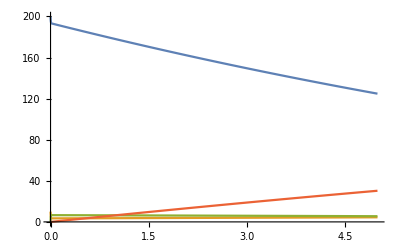

{{124.840085673165,4.4711793037518,5.5288206962482,30.3135866185134}}

```mathematica
ClearAll["Global`*"]
(*S -> 0, E+S <-> ES -> E+P*)
c={1/20,1, 100, 1};
eqns={s'[t]==-c[[1]]s[t]-c[[2]]e[t]s[t]+c[[3]]es[t],
e'[t]==-c[[2]]e[t]s[t]+c[[3]]es[t]+c[[4]]es[t],
es'[t]==c[[2]]e[t]s[t]-c[[3]]es[t]-c[[4]]es[t],
p'[t]==c[[4]]es[t],
s[0]==200,e[0]==10,es[0]==0,p[0]==0};
sol=NDSolve[eqns,{s,e,es,p},{t,0,5},StartingStepSize->1*^-8,MaxStepSize->1*^-4,PrecisionGoal->33,AccuracyGoal->33,WorkingPrecision->71,InterpolationOrder->All,MaxSteps->10^5];
Plot[Evaluate[{s[t],e[t],es[t],p[t]}/.sol],{t,0,5},PlotRange->{0,200}]
(*Plot[{s[t]/.sol,e[t]/.sol,es[t]/.sol,p[t]/.sol},{t,0,5}]*)
N[{s[t],e[t],es[t],p[t]}/.sol/.{t->5},15]
```